# Comment on “Climate consequences of hydrogen emissions” by Ocko and Hamburg (2022)

```mathematica
ClearAll["Global`*"]
```

## Parameters

### Parameters from Ocko and Hamburg (2022)

```mathematica
params =  {
	acapCO2-> 1.33 *10^-5 w/m2/ppb,
	a0->0.2173,a1->0.224, a2->0.282, a3->0.2763,
	tau1->394.4 yr,tau2->36.54 yr,tau3->4.304 yr, 
	acapCH4-> 3.88*10^-4 w/m2/ppb,
	tauCH4-> 11.8 yr, 
	f1->0.37,
	f2-> 0.106,
	tauH2-> 1.9 yr,
	ccap-> 3.5*10^-9 ppb/kg, 
	acapO3 -> 0.041 w/m2/du,
	acapH2O ->10^-4 w/m2/ppb,
	aCH4-> 1.46 * 10^-2 /yr,
	aO3-> 0.0056 du /ppb/yr,
	aH2O -> 0.042 /yr,
	tauO3->0.07 yr,
	tauH2O->8 yr
	}
```

{acapCO2→(0.0000133 w)/(m2 ppb),a0→0.2173,a1→0.224,a2→0.282,a3→0.2763,tau1→394.4 yr,tau2→36.54 yr,tau3→4.304 yr,acapCH4→(0.000388 w)/(m2 ppb),tauCH4→11.8 yr,f1→0.37,f2→0.106,tauH2→1.9 yr,ccap→(3.5×10^-9 ppb)/kg,acapO3→(0.041 w)/(du m2),acapH2O→w/(10000 m2 ppb),aCH4→0.0146/yr,aO3→(0.0056 du)/(ppb yr),aH2O→0.042/yr,tauO3→0.07 yr,tauH2O→8 yr}

```mathematica
params2 =  {
	acapCO2-> 1.33 *10^-5 ,
	a0->0.2173,a1->0.224, a2->0.282, a3->0.2763,
	tau1->394.4 ,tau2->36.54 ,tau3->4.304 , 
	acapCH4-> 3.88*10^-4 ,
	tauCH4-> 11.8 , 
	f1->0.37,
	f2-> 0.106,
	tauH2-> 1.9 ,
	ccap-> 3.5*10^-9 ,
	acapO3 -> 0.041 ,
	acapH2O ->10^-4 ,
	aCH4-> 1.46 * 10^-2 ,
	aO3-> 0.0056 ,
	aH2O -> 0.042 ,
	tauO3->0.07 ,
	tauH2O->8 
	}
```

{acapCO2→0.0000133,a0→0.2173,a1→0.224,a2→0.282,a3→0.2763,tau1→394.4,tau2→36.54,tau3→4.304,acapCH4→0.000388,tauCH4→11.8,f1→0.37,f2→0.106,tauH2→1.9,ccap→3.5×10^-9,acapO3→0.041,acapH2O→1/10000,aCH4→0.0146,aO3→0.0056,aH2O→0.042,tauO3→0.07,tauH2O→8}

```mathematica
params3 =  {
	acapCO2-> 1.33 *10^-5 ,
	a0->0.2173,a1->0.224, a2->0.282, a3->0.2763,
	tau1->394.4 ,tau2->36.54 ,tau3->4.304 , 
	acapCH4-> 3.88*10^-4 ,
	tauCH4-> 11.8 , 
	f1->0.37,
	f2-> 0.106,
	tauH2-> 1.4 ,
	ccap-> 3.5*10^-9 ,
	acapO3 -> 0.041 ,
	acapH2O ->10^-4 ,
	aCH4-> 1.46 * 10^-2 ,
	aO3-> 0.0056 ,
	aH2O -> 0.042 ,
	tauO3->0.07 ,
	tauH2O->8 
	}
params4 =  {
	acapCO2-> 1.33 *10^-5 ,
	a0->0.2173,a1->0.224, a2->0.282, a3->0.2763,
	tau1->394.4 ,tau2->36.54 ,tau3->4.304 , 
	acapCH4-> 3.88*10^-4 ,
	tauCH4-> 11.8 , 
	f1->0.37,
	f2-> 0.106,
	tauH2-> 2.5 ,
	ccap-> 3.5*10^-9 ,
	acapO3 -> 0.041 ,
	acapH2O ->10^-4 ,
	aCH4-> 1.46 * 10^-2 ,
	aO3-> 0.0056 ,
	aH2O -> 0.042 ,
	tauO3->0.07 ,
	tauH2O->8 
	}
```

{acapCO2→0.0000133,a0→0.2173,a1→0.224,a2→0.282,a3→0.2763,tau1→394.4,tau2→36.54,tau3→4.304,acapCH4→0.000388,tauCH4→11.8,f1→0.37,f2→0.106,tauH2→1.4,ccap→3.5×10^-9,acapO3→0.041,acapH2O→1/10000,aCH4→0.0146,aO3→0.0056,aH2O→0.042,tauO3→0.07,tauH2O→8}

{acapCO2→0.0000133,a0→0.2173,a1→0.224,a2→0.282,a3→0.2763,tau1→394.4,tau2→36.54,tau3→4.304,acapCH4→0.000388,tauCH4→11.8,f1→0.37,f2→0.106,tauH2→2.5,ccap→3.5×10^-9,acapO3→0.041,acapH2O→1/10000,aCH4→0.0146,aO3→0.0056,aH2O→0.042,tauO3→0.07,tauH2O→8}

### Other parameters required

```mathematica
H2 + 1/2 O2 --> H2O deltaH = 286 kJ/mol
CH4 + 2O2  --> CO2 + 2H2O  deltaH = 890 kJ/mol
CH4 --> C + 2 H2 deltaH = -74.8 kJ/mol
```

```mathematica
ppbperkgH2 = 3.5 * 10^-9 ppb/kg
molwtH2 = 0.002016 kg/mol
ppbpermol = ppbperkgH2 * molwtH2

molwtCH4 = 0.01604246 kg/mol
ppbperkgCH4 = ppbpermol/molwtCH4
molwtCO2 = 0.04401 kg/mol
ppbperkgCO2 = ppbpermol/molwtCO2
```

(3.5×10^-9 ppb)/kg

(0.002016 kg)/mol

(7.056×10^-12 ppb)/mol

(0.0160425 kg)/mol

(4.39833×10^-10 ppb)/kg

(0.04401 kg)/mol

(1.60327×10^-10 ppb)/kg

```mathematica
paramsFraming = {
	effCH4 -> 1, 
	effPyrolysis -> 1,
	effH2 -> 1,
	ch4DeltaH -> 890 kJ/mol,
	h2deltaH -> 286 kJ/mol,
	pyrolysisDeltaH -> -74.8 kJ/mol
	}
```

{effCH4→1,effPyrolysis→1,effH2→1,ch4DeltaH→(890 kJ)/mol,h2deltaH→(286 kJ)/mol,pyrolysisDeltaH→-(74.8 kJ)/mol}

```mathematica
reCO2 = 1.02 
reCH4Ratio = 1.10 / reCO2
reO3Ratio = 0.82 / reCO2
reH2ORatio = 0.96 / reCO2
```

1.02

1.07843

0.803922

0.941176

## Equations used in the main text

### Radiative forcing

#### Impulse

```mathematica
rfCo2 = (acapCO2 (a0+a1 ⅇ^(-t/tau1)+a2 ⅇ^(-t/tau2)+a3 ⅇ^(-t/tau3)))
rfCh4 = (acapCH4 ⅇ^(-t/tauCH4) (1+f1+f2))
rfH2 = ((1+f1+f2)*(acapCH4 aCH4 (ⅇ^(-t/tauCH4)-ⅇ^(-t/tauH2))  tauCH4 tauH2)/(tauCH4-tauH2) + (acapO3 aO3 (ⅇ^(-t/tauH2)-ⅇ^(-t/tauO3))  tauH2 tauO3)/(tauH2-tauO3) + (acapH2O aH2O (ⅇ^(-t/tauH2)-ⅇ^(-t/tauH2O))  tauH2 tauH2O)/(tauH2-tauH2O))
```

acapCO2 (a0+a1 ⅇ^(-t/tau1)+a2 ⅇ^(-t/tau2)+a3 ⅇ^(-t/tau3))

acapCH4 ⅇ^(-t/tauCH4) (1+f1+f2)

(acapCH4 aCH4 (ⅇ^(-t/tauCH4)-ⅇ^(-t/tauH2)) (1+f1+f2) tauCH4 tauH2)/(tauCH4-tauH2)+(acapH2O aH2O (ⅇ^(-t/tauH2)-ⅇ^(-t/tauH2O)) tauH2 tauH2O)/(tauH2-tauH2O)+(acapO3 aO3 (ⅇ^(-t/tauH2)-ⅇ^(-t/tauO3)) tauH2 tauO3)/(tauH2-tauO3)

#### Conversion of decayed CH4 to CO2

```mathematica
(* added CO2 at t-dis *)
decayCh4Ppb = ⅇ^(-t/tauCH4) /.params2 // Simplify
addedCo2PpbTimeT = D[decayCh4Ppb, t] * -1 // Simplify
addedCo2PpbTimeTDis = addedCo2PpbTimeT /.{t->t-dis} 
(* decay of CO2 added at t-dis to t *)
decayCO2 = acapCO2 * (a0+a1 ⅇ^(-t/tau1)+a2 ⅇ^(-t/tau2)+a3 ⅇ^(-t/tau3)) /.params2 // Simplify
decayCO2Dis = decayCO2/.{t->dis}
addedCo2RfTimeTDisDecay = addedCo2PpbTimeTDis * decayCO2Dis
(* Integrated effect *)
rfCo2Ch4 = Integrate[addedCo2RfTimeTDisDecay, {dis, 0, t}] // Simplify 
rfCh4New = (acapCH4 ⅇ^(-t/tauCH4) (1+f1+f2)) + rfCo2Ch4 /.params2 // Simplify
```

ⅇ^(-0.0847458 t)

0.0847458 ⅇ^(-0.0847458 t)

0.0847458 ⅇ^(-0.0847458 (-dis+t))

2.89009×10^-6+3.67479×10^-6 ⅇ^(-0.232342 t)+3.7506×10^-6 ⅇ^(-0.0273673 t)+2.9792×10^-6 ⅇ^(-0.0025355 t)

2.89009×10^-6+3.67479×10^-6 ⅇ^(-0.232342 dis)+3.7506×10^-6 ⅇ^(-0.0273673 dis)+2.9792×10^-6 ⅇ^(-0.0025355 dis)

0.0847458 ⅇ^(-0.0847458 (-dis+t)) (2.89009×10^-6+3.67479×10^-6 ⅇ^(-0.232342 dis)+3.7506×10^-6 ⅇ^(-0.0273673 dis)+2.9792×10^-6 ⅇ^(-0.0025355 dis))

2.89009×10^-6-2.10996×10^-6 ⅇ^(-0.232342 t)-9.3907×10^-6 ⅇ^(-0.0847458 t)+5.53949×10^-6 ⅇ^(-0.0273673 t)+3.07108×10^-6 ⅇ^(-0.0025355 t)

2.89009×10^-6-2.10996×10^-6 ⅇ^(-0.232342 t)+0.000563297 ⅇ^(-0.0847458 t)+5.53949×10^-6 ⅇ^(-0.0273673 t)+3.07108×10^-6 ⅇ^(-0.0025355 t)

#### Insert parameter values

```mathematica
rfCo2 /.params2
rfCh4 /.params2
rfH2 /.params2
rfH2/.params3//Simplify
rfH2/.params4//Simplify
```

0.0000133 (0.2173+0.2763 ⅇ^(-0.232342 t)+0.282 ⅇ^(-0.0273673 t)+0.224 ⅇ^(-0.0025355 t))

0.000572688 ⅇ^(-0.0847458 t)

0.0000166868 (-ⅇ^(-14.2857 t)+ⅇ^(-0.526316 t))-0.0000104656 (ⅇ^(-0.526316 t)-ⅇ^(-t/8))+0.0000189353 (-ⅇ^(-0.526316 t)+ⅇ^(-0.0847458 t))

-0.0000169179 ⅇ^(-14.2857 t)-3.49089×10^-6 ⅇ^(-0.714286 t)+7.12727×10^-6 ⅇ^(-0.125 t)+0.0000132815 ⅇ^(-0.0847458 t)

-0.000016535 ⅇ^(-14.2857 t)-0.00002526 ⅇ^(-0.4 t)+0.0000152727 ⅇ^(-0.125 t)+0.0000265222 ⅇ^(-0.0847458 t)

#### Sustained

```mathematica
rfCo2Sustained = Integrate[rfCo2/.params2, {t, 0, t}]//Simplify
rfCh4Sustained = Integrate[rfCh4/.params2, {t, 0, t}]//Simplify
rfH2Sustained = Integrate[rfH2/.params2, {t, 0, t}]//Simplify
rfH2P3Sustained = Integrate[rfH2/.params3, {t, 0, t}]//Simplify
rfH2P4Sustained = Integrate[rfH2/.params4, {t, 0, t}]//Simplify
```

0.00132786-0.0000158163 ⅇ^(-0.232342 t)-0.000137047 ⅇ^(-0.0273673 t)-0.001175 ⅇ^(-0.0025355 t)+2.89009×10^-6 t

0.00675772-0.00675772 ⅇ^(-0.0847458 t)

0.000281836+1.16807×10^-6 ⅇ^(-14.2857 t)+0.0000241567 ⅇ^(-0.526316 t)-0.0000837246 ⅇ^(-0.125 t)-0.000223436 ⅇ^(-0.0847458 t)

0.000207669+1.18425×10^-6 ⅇ^(-14.2857 t)+4.88725×10^-6 ⅇ^(-0.714286 t)-0.0000570182 ⅇ^(-0.125 t)-0.000156722 ⅇ^(-0.0847458 t)

0.000370837+1.15745×10^-6 ⅇ^(-14.2857 t)+0.0000631499 ⅇ^(-0.4 t)-0.000122182 ⅇ^(-0.125 t)-0.000312962 ⅇ^(-0.0847458 t)

```mathematica
rfCh4SustainedNew = Integrate[rfCh4New/.params2, {t, 0, t}]//Simplify
```

0.00805148+9.08129×10^-6 ⅇ^(-0.232342 t)-0.00664691 ⅇ^(-0.0847458 t)-0.000202413 ⅇ^(-0.0273673 t)-0.00121124 ⅇ^(-0.0025355 t)+2.89009×10^-6 t

### AGWP

#### Impulse

```mathematica
agwpCo2 = Integrate[rfCo2/.params2, {t, 0, H}]
agwpCh4 = Integrate[rfCh4/.params2, {t, 0, H}]
agwpH2 = Integrate[rfH2/.params2, {t, 0, H}]
agwpH2P3 = Integrate[rfH2/.params3, {t, 0, H}]//Simplify
agwpH2P4 = Integrate[rfH2/.params4, {t, 0, H}]//Simplify
```

0.00132786-0.0000158163 ⅇ^(-0.232342 H)-0.000137047 ⅇ^(-0.0273673 H)-0.001175 ⅇ^(-0.0025355 H)+2.89009×10^-6 H

0.00675772-0.00675772 ⅇ^(-0.0847458 H)

0.000281836+1.16807×10^-6 ⅇ^(-14.2857 H)+0.0000241567 ⅇ^(-0.526316 H)-0.0000837246 ⅇ^(-0.125 H)-0.000223436 ⅇ^(-0.0847458 H)

0.000207669+1.18425×10^-6 ⅇ^(-14.2857 H)+4.88725×10^-6 ⅇ^(-0.714286 H)-0.0000570182 ⅇ^(-0.125 H)-0.000156722 ⅇ^(-0.0847458 H)

0.000370837+1.15745×10^-6 ⅇ^(-14.2857 H)+0.0000631499 ⅇ^(-0.4 H)-0.000122182 ⅇ^(-0.125 H)-0.000312962 ⅇ^(-0.0847458 H)

#### Sustained

```mathematica
agwpCo2Sustained = Integrate[agwpCo2, {H, 0, H}]//Simplify
agwpCh4Sustained = Integrate[agwpCh4, {H, 0, H}]//Simplify
agwpH2Sustained = Integrate[agwpH2, {H, 0, H}]//Simplify
```

-0.468494+0.0000680733 ⅇ^(-0.232342 H)+0.00500769 ⅇ^(-0.0273673 H)+0.463419 ⅇ^(-0.0025355 H)+0.00132786 H+1.44505×10^-6 H^2

-0.0797411+0.0797411 ⅇ^(-0.0847458 H)+0.00675772 H

-0.00326036-8.17652×10^-8 ⅇ^(-14.2857 H)-0.0000458978 ⅇ^(-0.526316 H)+0.000669797 ⅇ^(-0.125 H)+0.00263655 ⅇ^(-0.0847458 H)+0.000281836 H

### Climate response

#### Equations from Gasser et al. 2017

```mathematica
climateResponseBR2008 = 1.06*(0.595/8.4*Exp[-t/8.4]+0.405/409.5*Exp[-t/409.5])
climateResponseG2013 = 0.885*(0.587/4.1*Exp[-t/4.1]+0.413/249*Exp[-t/249])
climateResponseO22 = 0.852*(0.572/3.5*Exp[-t/3.5]+0.428/166*Exp[-t/166])
```

1.06 (0.0708333 ⅇ^(-0.119048 t)+0.000989011 ⅇ^(-0.002442 t))

0.885 (0.143171 ⅇ^(-0.243902 t)+0.00165863 ⅇ^(-t/249))

0.852 (0.163429 ⅇ^(-0.285714 t)+0.00257831 ⅇ^(-t/166))

#### Equations from Caldeira and Myhrvold (2013)

```mathematica
tCumuRiseFraction2Exp = 1 - (theta0*Exp[-t/tau0] + theta1*Exp[-t/tau1])
tCumuResponseFraction2Exp = (theta0*Exp[-t/tau0] + theta1*Exp[-t/tau1])
climateResponseCM2013 = -1* eff * D[tCumuResponseFraction2Exp, t] /.{eff->6.70/6.79, theta0->0.551, tau0->3.62, theta1->0.449, tau1->219.0}
```

1-ⅇ^(-t/tau0) theta0-ⅇ^(-t/tau1) theta1

ⅇ^(-t/tau0) theta0+ⅇ^(-t/tau1) theta1

-0.986745 (-0.15221 ⅇ^(-0.276243 t)-0.00205023 ⅇ^(-0.00456621 t))

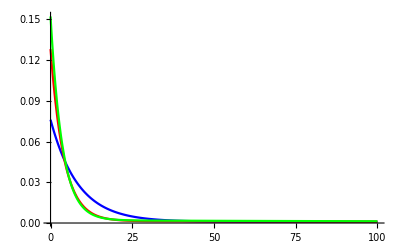

```mathematica
Plot[ {climateResponseBR2008, climateResponseG2013, climateResponseCM2013}, 
      {t, 0, 100}, PlotRange->All, PlotStyle->{Blue, Red, Green}]
```

## Apply parameters to equations

```mathematica
term1ClimateResponseG2013 = climateResponseG2013/.{t->H-t}
Integrate[term1ClimateResponseG2013 * rfCo2/.params2, {t, 0, H}] // Simplify
Integrate[term1ClimateResponseG2013 * rfCh4/.params2, {t, 0, H}] // Simplify
Integrate[term1ClimateResponseG2013 * rfH2/.params2, {t, 0, H}] // Simplify
Integrate[(term1ClimateResponseG2013 * rfH2)/.params3, {t, 0, H}] // Simplify
Integrate[(term1ClimateResponseG2013 * rfH2)/.params4, {t, 0, H}] // Simplify
Integrate[(term1ClimateResponseG2013 * rfCh4New)/.params2, {t, 0, H}] // Simplify
```

0.885 (0.143171 ⅇ^(-0.243902 (H-t))+0.00165863 ⅇ^(1/249 (-H+t)))

-0.0000455369 ⅇ^(-0.243902 H)+0.0000402533 ⅇ^(-0.232342 H)+1.9589×10^-6 ⅇ^(-0.0273673 H)-3.75064×10^-6 ⅇ^(-0.00401606 H)+4.51763×10^-6 ⅇ^(-0.0025355 H)+2.55773×10^-6 ⅇ^(-2.22045×10^-16 H)

-0.000455922 ⅇ^(-0.243902 H)+0.000445509 ⅇ^(-0.0847458 H)+0.0000104131 ⅇ^(-0.00401606 H)

1.52288×10^-7 ⅇ^(-14.2857 H)+5.73996×10^-6 ⅇ^(-0.526316 H)-0.0000320818 ⅇ^(-0.243902 H)+0.0000110255 ⅇ^(-0.125 H)+0.0000147302 ⅇ^(-0.0847458 H)+4.33827×10^-7 ⅇ^(-0.00401606 H)

1.54397×10^-7 ⅇ^(-14.2857 H)+9.47549×10^-7 ⅇ^(-0.714286 H)-0.0000192616 ⅇ^(-0.243902 H)+7.50857×10^-6 ⅇ^(-0.125 H)+0.000010332 ⅇ^(-0.0847458 H)+3.19017×10^-7 ⅇ^(-0.00401606 H)

1.50903×10^-7 ⅇ^(-14.2857 H)+0.0000205974 ⅇ^(-0.4 H)-0.0000580427 ⅇ^(-0.243902 H)+0.0000160898 ⅇ^(-0.125 H)+0.0000206323 ⅇ^(-0.0847458 H)+5.72215×10^-7 ⅇ^(-0.00401606 H)

-0.000431675 ⅇ^(-0.243902 H)-0.0000231123 ⅇ^(-0.232342 H)+0.000438204 ⅇ^(-0.0847458 H)+2.89322×10^-6 ⅇ^(-0.0273673 H)+6.47584×10^-6 ⅇ^(-0.00401606 H)+4.65696×10^-6 ⅇ^(-0.0025355 H)+2.55773×10^-6 ⅇ^(2.22045×10^-16 H)

```mathematica
term1ClimateResponseG2013 = climateResponseG2013/.{t->H-t}
Integrate[term1ClimateResponseG2013 * rfCo2Sustained/.{tp->H}/.params2, {t, 0, H}] // Simplify
Integrate[term1ClimateResponseG2013 * rfCh4Sustained/.{tp->H}/.params2, {t, 0, H}] // Simplify
Integrate[term1ClimateResponseG2013 * rfH2Sustained/.{tp->H}/.params2, {t, 0, H}] // Simplify
Integrate[term1ClimateResponseG2013 * rfH2P3Sustained/.{tp->H}/.params3, {t, 0, H}] // Simplify
Integrate[term1ClimateResponseG2013 * rfH2P4Sustained/.{tp->H}/.params4, {t, 0, H}] // Simplify
Integrate[term1ClimateResponseG2013 * rfCh4SustainedNew/.{tp->H}/.params2, {t, 0, H}] // Simplify
```

0.885 (0.143171 ⅇ^(-0.243902 (H-t))+0.00165863 ⅇ^(1/249 (-H+t)))

0.000186701 ⅇ^(-0.243902 H)-0.00017325 ⅇ^(-0.232342 H)-0.0000715784 ⅇ^(-0.0273673 H)+0.00093391 ⅇ^(-0.00401606 H)-0.00178175 ⅇ^(-0.0025355 H)+ⅇ^(-2.22045×10^-16 H) (0.000905971+2.55773×10^-6 H)

0.00598058+0.00186928 ⅇ^(-0.243902 H)-0.00525701 ⅇ^(-0.0847458 H)-0.000122874 ⅇ^(-0.00401606 H)-0.00246998 ⅇ^(-H/249)

0.000249425-1.06602×10^-8 ⅇ^(-14.2857 H)-0.0000109059 ⅇ^(-0.526316 H)+0.000131535 ⅇ^(-0.243902 H)-0.0000882037 ⅇ^(-0.125 H)-0.000173817 ⅇ^(-0.0847458 H)-0.000108023 ⅇ^(-0.00401606 H)

0.000183787-1.08078×10^-8 ⅇ^(-14.2857 H)-1.32657×10^-6 ⅇ^(-0.714286 H)+0.0000789724 ⅇ^(-0.243902 H)-0.0000600685 ⅇ^(-0.125 H)-0.000121918 ⅇ^(-0.0847458 H)-0.0000794351 ⅇ^(-0.00401606 H)

0.00032819-1.05632×10^-8 ⅇ^(-14.2857 H)-0.0000514936 ⅇ^(-0.4 H)+0.000237975 ⅇ^(-0.243902 H)-0.000128718 ⅇ^(-0.125 H)-0.000243462 ⅇ^(-0.0847458 H)-0.000142481 ⅇ^(-0.00401606 H)

0.00176987 ⅇ^(-0.243902 H)+0.0000994755 ⅇ^(-0.232342 H)-0.00517081 ⅇ^(-0.0847458 H)-0.000105718 ⅇ^(-0.0273673 H)-0.00161248 ⅇ^(-0.00401606 H)-0.00183671 ⅇ^(-0.0025355 H)+ⅇ^(2.22045×10^-16 H) (0.00685637+2.55773×10^-6 H)

#### Other response function

```mathematica
term1ClimateResponseBR2008 = climateResponseBR2008/.{t->H-t}
term1ClimateResponseO22 = climateResponseO22/.{t->H-t}
term1ClimateResponseCM2013 = climateResponseCM2013/.{t->H-t}
```

1.06 (0.0708333 ⅇ^(-0.119048 (H-t))+0.000989011 ⅇ^(-0.002442 (H-t)))

0.852 (0.163429 ⅇ^(-0.285714 (H-t))+0.00257831 ⅇ^(1/166 (-H+t)))

-0.986745 (-0.15221 ⅇ^(-0.276243 (H-t))-0.00205023 ⅇ^(-0.00456621 (H-t)))

```mathematica
Integrate[term1ClimateResponseBR2008 * rfCo2/.params2, {t, 0, H}] // Simplify
Integrate[term1ClimateResponseO22 * rfCo2/.params2, {t, 0, H}] // Simplify
Integrate[term1ClimateResponseCM2013 * rfCo2/.params2, {t, 0, H}] // Simplify

Integrate[term1ClimateResponseBR2008 * rfCo2Sustained/.{tp->H}/.params2, {t, 0, H}] // Simplify
Integrate[term1ClimateResponseO22 * rfCo2Sustained/.{tp->H}/.params2, {t, 0, H}] // Simplify
Integrate[term1ClimateResponseCM2013 * rfCo2Sustained/.{tp->H}/.params2, {t, 0, H}] // Simplify
```

-2.45214×10^-6 ⅇ^(-0.232342 H)-4.37889×10^-6 ⅇ^(-0.119048 H)+2.91387×10^-6 ⅇ^(-0.0273673 H)-0.0000314858 ⅇ^(-0.0025355 H)+0.0000323395 ⅇ^(-0.002442 H)+3.0635×10^-6 ⅇ^(1.11022×10^-16 H)

2.46236×10^-6-0.0000144819 ⅇ^(-0.285714 H)+9.55137×10^-6 ⅇ^(-0.232342 H)+1.63543×10^-6 ⅇ^(-0.0273673 H)-2.50815×10^-6 ⅇ^(-0.0060241 H)+3.34086×10^-6 ⅇ^(-0.0025355 H)

2.85178×10^-6-0.0000180416 ⅇ^(-0.276243 H)+0.0000125394 ⅇ^(-0.232342 H)+1.93065×10^-6 ⅇ^(-0.0273673 H)-3.883×10^-6 ⅇ^(-0.00456621 H)+4.60275×10^-6 ⅇ^(-0.0025355 H)

0.000010554 ⅇ^(-0.232342 H)+0.0000367827 ⅇ^(-0.119048 H)-0.000106473 ⅇ^(-0.0273673 H)+0.012418 ⅇ^(-0.0025355 H)-0.013243 ⅇ^(-0.002442 H)+ⅇ^(1.11022×10^-16 H) (0.000884147+3.0635×10^-6 H)

0.000951461+0.0000506865 ⅇ^(-0.285714 H)-0.0000411091 ⅇ^(-0.232342 H)-0.0000597587 ⅇ^(-0.0273673 H)+0.000416354 ⅇ^(-0.0060241 H)-0.00131763 ⅇ^(-0.0025355 H)+2.46236×10^-6 H

0.00102415+0.0000653105 ⅇ^(-0.276243 H)-0.0000539695 ⅇ^(-0.232342 H)-0.0000705459 ⅇ^(-0.0273673 H)+0.000850376 ⅇ^(-0.00456621 H)-0.00181532 ⅇ^(-0.0025355 H)+2.85178×10^-6 H

```mathematica
Integrate[term1ClimateResponseBR2008 * rfCh4/.params2, {t, 0, H}] // Simplify
Integrate[term1ClimateResponseO22 * rfCh4/.params2, {t, 0, H}] // Simplify
Integrate[term1ClimateResponseCM2013 * rfCh4/.params2, {t, 0, H}] // Simplify

Integrate[term1ClimateResponseBR2008 * rfCh4Sustained/.{tp->H}/.params2, {t, 0, H}] // Simplify
Integrate[term1ClimateResponseO22 * rfCh4Sustained/.{tp->H}/.params2, {t, 0, H}] // Simplify
Integrate[term1ClimateResponseCM2013 * rfCh4Sustained/.{tp->H}/.params2, {t, 0, H}] // Simplify
```

-0.00125356 ⅇ^(-0.119048 H)+0.00124626 ⅇ^(-0.0847458 H)+7.29467×10^-6 ⅇ^(-0.002442 H)

-0.000396787 ⅇ^(-0.285714 H)+0.000380806 ⅇ^(-0.0847458 H)+0.0000159808 ⅇ^(-0.0060241 H)

-0.000449162 ⅇ^(-0.276243 H)+0.000434713 ⅇ^(-0.0847458 H)+0.0000144498 ⅇ^(-0.00456621 H)

0.00716318+0.0105299 ⅇ^(-0.119048 H)-0.0147059 ⅇ^(-0.0847458 H)-0.00298717 ⅇ^(-0.002442 H)

0.00575758+0.00138876 ⅇ^(-0.285714 H)-0.00449351 ⅇ^(-0.0847458 H)-0.000188574 ⅇ^(-0.0060241 H)-0.00246424 ⅇ^(-H/166)

0.00666815+0.00162597 ⅇ^(-0.276243 H)-0.00512961 ⅇ^(-0.0847458 H)-0.00316451 ⅇ^(-0.00456621 H)

```mathematica
Integrate[term1ClimateResponseBR2008 * rfH2/.params2, {t, 0, H}] // Simplify
Integrate[term1ClimateResponseO22 * rfH2/.params2, {t, 0, H}] // Simplify
Integrate[term1ClimateResponseCM2013 * rfH2/.params2, {t, 0, H}] // Simplify

Integrate[term1ClimateResponseBR2008 * rfH2Sustained/.{tp->H}/.params2, {t, 0, H}] // Simplify
Integrate[term1ClimateResponseO22 * rfH2Sustained/.{tp->H}/.params2, {t, 0, H}] // Simplify
Integrate[term1ClimateResponseCM2013 * rfH2Sustained/.{tp->H}/.params2, {t, 0, H}] // Simplify
```

8.96647×10^-8 ⅇ^(-14.2857 H)+2.36939×10^-6 ⅇ^(-0.526316 H)-0.000132102 ⅇ^(-0.125 H)+0.000088133 ⅇ^(-0.119048 H)+0.0000412062 ⅇ^(-0.0847458 H)+3.04044×10^-7 ⅇ^(-0.002442 H)

1.6853×10^-7 ⅇ^(-14.2857 H)+7.41157×10^-6 ⅇ^(-0.526316 H)-0.0000297104 ⅇ^(-0.285714 H)+8.87403×10^-6 ⅇ^(-0.125 H)+0.0000125909 ⅇ^(-0.0847458 H)+6.65372×10^-7 ⅇ^(-0.0060241 H)

1.81259×10^-7 ⅇ^(-14.2857 H)+7.6853×10^-6 ⅇ^(-0.526316 H)-0.0000330588 ⅇ^(-0.276243 H)+0.0000102171 ⅇ^(-0.125 H)+0.0000143733 ⅇ^(-0.0847458 H)+6.01905×10^-7 ⅇ^(-0.00456621 H)

0.000298746-6.27653×10^-9 ⅇ^(-14.2857 H)-4.50184×10^-6 ⅇ^(-0.526316 H)+0.00105682 ⅇ^(-0.125 H)-0.000740317 ⅇ^(-0.119048 H)-0.000486233 ⅇ^(-0.0847458 H)-0.000124506 ⅇ^(-0.002442 H)

0.000240124-1.17971×10^-8 ⅇ^(-14.2857 H)-0.000014082 ⅇ^(-0.526316 H)+0.000103986 ⅇ^(-0.285714 H)-0.0000709922 ⅇ^(-0.125 H)-0.000148573 ⅇ^(-0.0847458 H)-0.000110452 ⅇ^(-0.0060241 H)

0.0002781-1.26881×10^-8 ⅇ^(-14.2857 H)-0.0000146021 ⅇ^(-0.526316 H)+0.000119673 ⅇ^(-0.276243 H)-0.0000817366 ⅇ^(-0.125 H)-0.000169605 ⅇ^(-0.0847458 H)-0.000131817 ⅇ^(-0.00456621 H)